## ECO 6108 Han Sun 6986498 Assignment 3

1. Find a continuous function c:t→c_t,0≤t≤1, to 
	minimize_((c_t)_(0≤t≤1))1/4∫_0^1 c_t^4 ⅆt 
	subject to (d x)/(d t)=x_t + c_t, x_0=(x̄)_0,x_1=0.

The Hamiltonian is

```mathematica
ℋ=1/4 c^4+λ (x+c)
```

c^4/4+(c+x) λ

The first-order condition for minimizing the Hamiltonian is

```mathematica
foc=D[ℋ,c]==0
```

c^3+λ==0

The optimal control at time t

```mathematica
foc=foc/.λ-> λ[t]
```

c^3+λ[t]==0

```mathematica
s[0]=Solve[foc,c]
```

{{c→-λ[t]^(1/3)},{c→(-1)^(1/3) λ[t]^(1/3)},{c→-(-1)^(2/3) λ[t]^(1/3)}}

Note that the three solutions are the same. So, any one of them will do.

```mathematica
s[1]=s[0][[1]]
```

{c→-λ[t]^(1/3)}

```mathematica
c[t_]:=Evaluate[c/.s[1]]
```

```mathematica
c[t]
```

-λ[t]^(1/3)

```mathematica
c[1]
```

-λ[1]^(1/3)

The adjoint equation is

```mathematica
eq[1]=λ'[t]==-(D[ℋ,x]/.{x-> x[t],λ-> λ[t],c-> c[t]})
```

λ'[t]==-λ[t]

```mathematica
s[2]=DSolve[{eq[1],λ[0]==λ0},λ[t],t]//Flatten
```

{λ[t]→ⅇ^-t λ0}

```mathematica
λ[t_]:=Evaluate[λ[t]/.s[2]]
```

```mathematica
λ[t]
```

ⅇ^-t λ0

```mathematica
λ[0]
```

λ0

The state equation is

```mathematica
eq[2]=x'[t]==x[t]+c[t]
```

x'[t]==-(ⅇ^-t λ0)^(1/3)+x[t]

```mathematica
eq[2]=eq[2]//PowerExpand
```

x'[t]==-ⅇ^(-t/3) λ0^(1/3)+x[t]

```mathematica
s[3]=DSolve[{eq[2],x[1]==0},x[t],t]//Flatten
```

{x[t]→3/4 ⅇ^(-4/3-t/3) (ⅇ^(4/3)-ⅇ^(4 t/3)) λ0^(1/3)}

```mathematica
s[3]=s[3]//FullSimplify
```

{x[t]→3/4 ⅇ^(-t/3) (1-ⅇ^(4/3 (-1+t))) λ0^(1/3)}

```mathematica
x[t_]:=Evaluate[x[t]/.s[3]]
```

```mathematica
x[t]
```

3/4 ⅇ^(-t/3) (1-ⅇ^(4/3 (-1+t))) λ0^(1/3)

```mathematica
x[0]
```

3/4 (1-1/ⅇ^(4/3)) λ0^(1/3)

The initial condition for the state of the system is

```mathematica
eq[3]=x[0]==x0
```

3/4 (1-1/ⅇ^(4/3)) λ0^(1/3)==x0

```mathematica
s[4]=Solve[eq[3],λ0]//Flatten
```

{λ0→(64 (3 ⅇ^(16/3) x0^3+6 ⅇ^(20/3) x0^3+6 ⅇ^(28/3) x0^3+3 ⅇ^(32/3) x0^3+1/64 (64 ⅇ^4+448 ⅇ^8+64 ⅇ^12) x0^3))/(-27+81 ⅇ^4-81 ⅇ^8+27 ⅇ^12)}

```mathematica
s[4]=s[4]//FullSimplify
```

{λ0→(64 ⅇ^4 x0^3)/(27 (-1+ⅇ^(4/3))^3)}

The initial value of the adjoint variable is

```mathematica
λ0=λ0/.s[4]
```

(64 ⅇ^4 x0^3)/(27 (-1+ⅇ^(4/3))^3)

The optimal control at time t is

```mathematica
c[t]
```

-(4 (ⅇ^(4-t) x0^3)^(1/3))/(3 (-1+ⅇ^(4/3)))

The minimum cost is

```mathematica
v=1/4 ∫_0^1 c[t]^4 ⅆt
```

(16 ⅇ^4 (x0^3)^(4/3))/(27 (-1+ⅇ^(4/3))^3)

```mathematica
v=v//PowerExpand
```

(16 ⅇ^4 x0^4)/(27 (-1+ⅇ^(4/3))^3)

```mathematica
ClearAll[ℋ,x,c,λ,x0,λ0,v,s,eq,foc]
```

2.  Solve the following cake-eating  problem with bequest:
	max_((c_t)_(0≤ t≤ T)) ∫_0^T ⅇ^(-δ t)u[c_t]ⅆt+ⅇ^(-δ T)ω[x_T],
	subject to dx/dt=-c_t,
c_t≥ 0,0≤ t≤ T,
x_0 is given, x_T≥ 0,

for the case   u[c]=1/(1-γ) c^(1-γ) and ω[x]=ϵ 1/(1-γ) x^(1-γ),  with γ=a positive  parameter less than 1 and ϵ a positive parameter.

The instantaneous utility function is

```mathematica
u[c_]:=1/(1-γ) c^(1-γ)
```

```mathematica
u[c]
```

c^(1-γ)/(1-γ)

The Hamiltonian is

```mathematica
ℋ=ⅇ^(-δ t) u[c]+λ (-c)
```

(c^(1-γ) ⅇ^(-t δ))/(1-γ)-c λ

The adjoint equation is

```mathematica
eq[1]=λ'[t]==(-D[ℋ,x]/.{x-> x[t],c-> c[t],λ-> λ[t]})
```

λ'[t]==0

Because dλ/dt=0, we must have λ[t]=λ=constant, 0≤ t≤ T.

The first-order condition that characterizes the optimal consumption at time t,0≤ t≤ T, is

```mathematica
foc=D[ℋ,c]==0
```

c^-γ ⅇ^(-t δ)-λ==0

The optimal consumption at time t,0≤ t≤ T, is

```mathematica
s[0]=Solve[foc,c]//Flatten
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{c→(ⅇ^(t δ) λ)^(-1/γ)}

```mathematica
c[t_]:=Evaluate[c/.s[0]//PowerExpand]
```

```mathematica
c[t]
```

ⅇ^(-(t δ)/γ) λ^(-1/γ)

```mathematica
c[0]
```

λ^(-1/γ)

The bequest is

```mathematica
x[T]=x0-∫_0^T c[t]ⅆt
```

x0-((γ-ⅇ^(-(T δ)/γ) γ) λ^(-1/γ))/δ

Now if the individual begins at time T (at the end of the time horizon) with x_T as the remaining cake, then there is no instantaneous payoff. The only payoff is the terminal payoff obtained from the bequest. In this case, we have
	v[x_T,T]=ⅇ^(-δ T)ω[x_T]
	=ϵ ⅇ^(-δ T)1/(1-γ) x_T^(1-γ).
Thus, the shadow price of cake at time T is
	D_1 v[x_T,T]=ϵ ⅇ^(-δ T) x_T^-γ=λ.

```mathematica
ω[x_]:=ϵ 1/(1-γ) x^(1-γ)
```

```mathematica
ω[x]
```

(x^(1-γ) ϵ)/(1-γ)

```mathematica
ω'[x]
```

x^-γ ϵ

```mathematica
ω[x[T]]
```

(ϵ (x0-((γ-ⅇ^(-(T δ)/γ) γ) λ^(-1/γ))/δ)^(1-γ))/(1-γ)

```mathematica
ω'[x[T]]
```

ϵ (x0-((γ-ⅇ^(-(T δ)/γ) γ) λ^(-1/γ))/δ)^-γ

```mathematica
eq[1]=λ==ⅇ^(-δ T) ω'[x[T]]
```

λ==ⅇ^(-T δ) ϵ (x0-((γ-ⅇ^(-(T δ)/γ) γ) λ^(-1/γ))/δ)^-γ

We need to solve eq[1] for λ. However, Mathematica cannot solve this equation under the current form. We need to transform it into a more amenable form.

```mathematica
eq[1][[2]]
```

ⅇ^(-T δ) ϵ (x0-((γ-ⅇ^(-(T δ)/γ) γ) λ^(-1/γ))/δ)^-γ

```mathematica
eq[1][[1]]
```

λ

```mathematica
eq[2]=(eq[1][[1]])^(-1/γ)==(eq[1][[2]])^(-1/γ)
```

λ^(-1/γ)==(ⅇ^(-T δ) ϵ (x0-1/δ(γ-ⅇ^(-(T δ)/γ) γ) λ^(-1/γ))^-γ)^(-1/γ)

```mathematica
eq[2]=eq[2]//PowerExpand
```

λ^(-1/γ)==ⅇ^((T δ)/γ) ϵ^(-1/γ) (x0-((γ-ⅇ^(-(T δ)/γ) γ) λ^(-1/γ))/δ)

Now let us represent λ^(-1/γ) by a.

```mathematica
eq[2]=eq[2]/.λ^(-1/γ)-> a
```

a==ⅇ^((T δ)/γ) (x0-(a (γ-ⅇ^(-(T δ)/γ) γ))/δ) ϵ^(-1/γ)

We now have a linear equation a, and this equation can be solved by Mathematica.

```mathematica
s[0]=Solve[eq[2],a]//Flatten
```

{a→(ⅇ^((T δ)/γ) x0 δ)/(-γ+ⅇ^((T δ)/γ) γ+δ ϵ^(1/γ))}

```mathematica
a=a/.s[0]
```

(ⅇ^((T δ)/γ) x0 δ)/(-γ+ⅇ^((T δ)/γ) γ+δ ϵ^(1/γ))

```mathematica
eq[3]=a==λ^(-1/γ)
```

(ⅇ^((T δ)/γ) x0 δ)/(-γ+ⅇ^((T δ)/γ) γ+δ ϵ^(1/γ))==λ^(-1/γ)

```mathematica
s[1]=Solve[eq[3],λ]//Flatten
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{λ→(-(ⅇ^((T δ)/γ) x0 δ)/(γ-ⅇ^((T δ)/γ) γ-δ ϵ^(1/γ)))^-γ}

The shadow price of cake is

```mathematica
λ=λ/.s[1]
```

(-(ⅇ^((T δ)/γ) x0 δ)/(γ-ⅇ^((T δ)/γ) γ-δ ϵ^(1/γ)))^-γ

The optimal consumption at time t

```mathematica
c[t]
```

ⅇ^(-(t δ)/γ) ((-(ⅇ^((T δ)/γ) x0 δ)/(γ-ⅇ^((T δ)/γ) γ-δ ϵ^(1/γ)))^-γ)^(-1/γ)

```mathematica
m[t_]:=u[c[t]]//PowerExpand
```

```mathematica
m[t]
```

1/(1-γ)(-1)^(1-γ) ⅇ^(-(t (1-γ) δ)/γ+(T (1-γ) δ)/γ) x0^(1-γ) δ^(1-γ) (γ-ⅇ^((T δ)/γ) γ-δ ϵ^(1/γ))^(-1+γ)

The optimal payoff

```mathematica
v=∫_0^T ⅇ^(-δ t) m[t]ⅆt+(ⅇ^(-δ T) ω[x[T]]//PowerExpand)
```

1/(-1+γ)(-1)^-γ ⅇ^(-T δ) (-1+ⅇ^((T δ)/γ)) x0^(1-γ) γ δ^-γ (γ-ⅇ^((T δ)/γ) γ-δ ϵ^(1/γ))^(-1+γ)+1/(1-γ)ⅇ^(-T δ) ϵ (x0+(ⅇ^((T δ)/γ) x0 (γ-ⅇ^(-(T δ)/γ) γ))/(γ-ⅇ^((T δ)/γ) γ-δ ϵ^(1/γ)))^(1-γ)

```mathematica
γ=0.5;δ=0.05;x0=1.0;T=1.0;ϵ=1;
```

```mathematica
v
```

2.72504+1.71066×10^-16 ⅈ

```mathematica
%//Chop
```

2.72504

```mathematica
ClearAll[u,ω,s,eq,λ,v,c,m,a,x,foc,ℋ,γ,δ,ϵ,T,x0]
```

3.  Find a continuous function c:t→c_t,0≤t≤2, to
	maximize_((c_t)_(0≤t≤2))∫_0^2 (2 x_t-3 c_t-c_t^2)ⅆt
subject to (d x)/(d t)=x_t + c_t,  x_0=5.

Let
(1(	v[ξ,τ]=maximize_((c_t)_(τ≤t≤2))∫_τ^2 (2 x_t-3 c_t-c_t^2)ⅆt
subject to (d x)/(d t)=x_t + c_t,  x_τ=ξ. 	

As defined, v[ξ,τ] gives the vallue attained by the objective function, given that the system begins at time 0≤ τ≤ 2 instate ξ. For τ=2, we have v[ξ,2]=0 because the integral in (2) is equal to 0. It follows from v[ξ,2]=0 that D_1 v[ξ,2]=0.

Let c_t^* be the optimal control at time t,0≤ t≤ 2, for the original problem and x_t^*,0≤ t≤ 2, be the state of the system at time t under the optimal control c_t^*,0≤ t≤ 2. Also, let λ_t=D_1 v[x_t^*,t] denote the co-state at time t along the optimal trajectory. 

The Hamiltonian is

```mathematica
ℋ=2 x-3 c-c^2+λ (x+c)
```

-3 c-c^2+2 x+(c+x) λ

The state equation is

```mathematica
eq[1]=x'[t]==x[t]+c[t]
```

x'[t]==c[t]+x[t]

The adjoint equation is

```mathematica
eq[2]=λ'[t]==(-D[ℋ,x]/.{x-> x[t],c-> c[t],λ-> λ[t]})
```

λ'[t]==-2-λ[t]

Now using the definition of λ_t=D_1 v[x_t^*,t], we have λ_2=0. Using this final condition, we can solve the adjoint equation to obtain:

```mathematica
s[0]=DSolve[{eq[2],λ[2]==0},λ[t],t]//Flatten//FullSimplify
```

{λ[t]→-2+2 ⅇ^(2-t)}

```mathematica
λ[t_]:=Evaluate[λ[t]/.s[0]]
```

```mathematica
λ[t]
```

-2+2 ⅇ^(2-t)

```mathematica
λ[0]
```

-2+2 ⅇ^2

The optimal control at each instant is obtained by maximizing the Hamiltonian ℋ[x_t^*,c,λ_t,t] at that instant. The first-order condition that characterizes c_t^* is

```mathematica
foc=(D[ℋ,c]==0)/.{x-> x[t],λ-> λ[t]}
```

-5-2 c+2 ⅇ^(2-t)==0

```mathematica
s[1]=Solve[foc,c]//Flatten//FullSimplify
```

{c→-5/2+ⅇ^(2-t)}

```mathematica
c[t_]:=Evaluate[c/.s[1]]
```

```mathematica
c[t]
```

-5/2+ⅇ^(2-t)

```mathematica
c[0]
```

-5/2+ⅇ^2

```mathematica
eq[1]
```

x'[t]==-5/2+ⅇ^(2-t)+x[t]

```mathematica
s[2]=DSolve[{eq[1],x[0]==5},x[t],t]//Flatten
```

{x[t]→1/2 ⅇ^-t (-ⅇ^2+5 ⅇ^t+5 ⅇ^(2 t)+ⅇ^(2+2 t))}

```mathematica
x[t_]:=Evaluate[x[t]/.s[2]]
```

```mathematica
x[t]
```

1/2 ⅇ^-t (-ⅇ^2+5 ⅇ^t+5 ⅇ^(2 t)+ⅇ^(2+2 t))

```mathematica
v=∫_0^2 (2 x[t]-3 c[t]-c[t]^2)ⅆt
```

7+5 ⅇ^2+ⅇ^4/2

```mathematica
ClearAll[ℋ,eq,s,λ,foc,s,c,x,v]
```

4.  Solve the following cake-eating  problem with addiction:
	max_((c_t)_(0≤ t≤ T)) ∫_0^T ⅇ^(-δ t-∫_0^t c_s ⅆs)u[c_t]ⅆt
	subject to 
		c_t≥ 0,0≤ t≤ T,
∫_0^T c_t ⅆt=x_0.
In solving the problem, use u[c]=Log[c], δ=0.05, T=1.0, and x_0=1.

```mathematica
u=Log[c]
```

Log[c]

```mathematica
ℋ=ⅇ^(-x0+x-δ t)u-λ c
```

-c λ+ⅇ^(x-x0-t δ) Log[c]

```mathematica
foc=D[ℋ, c]==0
```

ⅇ^(x-x0-t δ)/c-λ==0

```mathematica
s[0]=Solve[foc,c]//Flatten
```

{c→ⅇ^(x-x0-t δ)/λ}

```mathematica
c[t_]:=Evaluate[(c/.s[0])/.{x-> x[t],λ-> λ[t]}]
```

```mathematica
c[t]
```

ⅇ^(-x0-t δ+x[t])/λ[t]

```mathematica
c[0]
```

ⅇ^(-x0+x[0])/λ[0]

```mathematica
eq[1]=x'[t]==-c[t]
```

x'[t]==-ⅇ^(-x0-t δ+x[t])/λ[t]

```mathematica
D[ℋ, x]
```

ⅇ^(x-x0-t δ) Log[c]

```mathematica
D[ℋ, x]/.{c-> c[t],x-> x[t]}
```

ⅇ^(-x0-t δ+x[t]) Log[ⅇ^(-x0-t δ+x[t])/λ[t]]

```mathematica
eq[2]=λ'[t]==-%
```

λ'[t]==-ⅇ^(-x0-t δ+x[t]) Log[ⅇ^(-x0-t δ+x[t])/λ[t]]

```mathematica
eq[2]=eq[2]//PowerExpand
```

λ'[t]==-ⅇ^(-x0-t δ+x[t]) (-x0-t δ-Log[λ[t]]+x[t])

#### Numerical solution by NDsolve of Mathematica

```mathematica
x0=1.0;δ=0.05;T=1.0;
```

```mathematica
solution[λ0_]:=NDSolve[{eq[1],eq[2],x[0]==x0,λ[0]==λ0},{x,λ},{t,0,T}]//Flatten
```

```mathematica
xT[λ0_]:=x[T]/.solution[λ0]
```

#### The secant method to find λ_0 so that x_T=0

Finding the initial values of λ_0 to start the algorithm

```mathematica
xT[2]
```

0.656448

```mathematica
xT[1]
```

0.367661

```mathematica
xT[0.6]
```

-0.0594753

```mathematica
xT[0.65]
```

0.0313104

```mathematica
xT[0.63]
```

-0.00258777

```mathematica
xT[0.64]
```

0.0147249

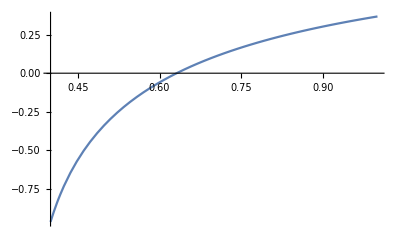

```mathematica
Plot[xT[λ0],{λ0,0.4,1}]
```

The value of λ_0 is bracketed between 0.60 and 0.65.

#### The secant algorithm

```mathematica
{ξ,η}={0.6,0.7};While[Abs[ξ-η]>10^-6,Which[xT[(ξ xT[η]-η xT[ξ])/(xT[η]-xT[ξ])]<0,ξ=(ξ xT[η]-η xT[ξ])/(xT[η]-xT[ξ]),xT[(ξ xT[η]-η xT[ξ])/(xT[η]-xT[ξ])]>0,η=(ξ xT[η]-η xT[ξ])/(xT[η]-xT[ξ]),xT[(ξ xT[η]-η xT[ξ])/(xT[η]-xT[ξ])]=0,ξ=η=xT[(ξ xT[η]-η xT[ξ])/(xT[η]-xT[ξ])]]];
{ξ,η}
```

{0.631467,0.631467}

The shadow price of cake at time 0

```mathematica
λ0=ξ
```

0.631467

```mathematica
xT[λ0]
```

-2.78809×10^-16

```mathematica
%//Chop
```

0

```mathematica
solutionoptimal=solution[λ0]
```

{x→InterpolatingFunction[{{0., 1.}}, <>],λ→InterpolatingFunction[{{0., 1.}}, <>]}

```mathematica
c[t_]:=Evaluate[c[t]/.solutionoptimal]
```

```mathematica
c[1]
```

0.578265

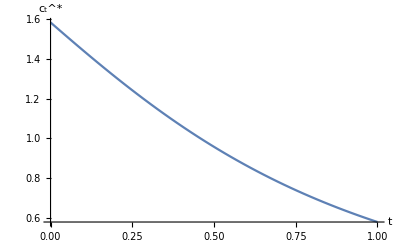

```mathematica
Plot[c[t],{t,0,T},AxesLabel-> {"t","c_t^*"}]
```

```mathematica
∫_0^T c[t]ⅆt//N
```

1.

```mathematica
x[t_]:=Evaluate[x[t]/.solutionoptimal]
```

```mathematica
x[0]
```

1.

```mathematica
x[1]
```

-2.78809×10^-16

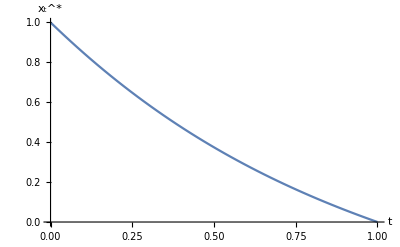

```mathematica
Plot[x[t],{t,0,T},AxesLabel->{"t","x_t^*"}]
```

```mathematica
λ[t_ ]:=Evaluate[λ[t]/.solutionoptimal]
```

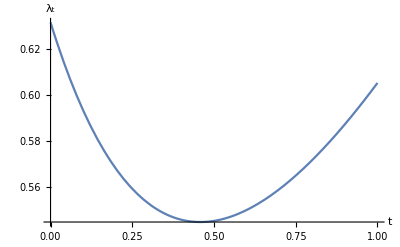

```mathematica
Plot[λ[t],{t,0,T},AxesLabel->{"t","λ_t"}]
```

```mathematica
v=∫_0^T ⅇ^(-δ t-(x[0]-x[t])) Log[c[t]]ⅆt//N
```

0.0263163

```mathematica
ClearAll[u,c,ℋ,foc,eq,s,solution,solutionoptimal,v,x,xT,λ,λ0,ξ,η,δ,x0,T];
```

5.  Consider the following q problem in continuous time:
	
	(v[K)_0,0]=max_((I_t)_(t≥ 0)) ∫_0^∞ ⅇ^(-r t)(A_t F[K_t]-I_t-1/2 χ I_t^2/K_t)ⅆt
	   subject to  (d K)/(d t)=I_t,  K_0  is given. 

Here r is the interest rate. Note that in the problem just stated the capital stock cannot be adjusted instantaneously without incurring prohibitive adjustment costs. More precisely, if I_t is the amount of capital invested (or dis-invested), then the total cost of investment is given by I_t+1/2(χ I_t^2)/K_t, where χ is a positive constant.     

(a)  Does the model you have a stationary equilibrium? If your answer is affirmative, draw a phase diagram to explain the convergence to the stationary equilibrium.
(b)  Show that the value of the Hamiltonian -  evaluated at each instant t along the optimal trajectory -  gives the permanent level of utility, i.e., the permanent level of real income, of the representative agent from instant t on until the end of time.

(a) Let I_t^*,t≥ 0, denote the firm’s optimal investment program and K_t^* denote the firm’s capital stock under the optimal investment program. We have
(1)	dK^*/dt=I_t^*,K_0^*=K_0.

To find I_t^* and K_t^*, define the current Hamiltonian

	ℋ̃[K,I,λ̃,t]=A_t F[K]-I-1/2 χ I^2/K+λ̃ I.
The adjoint equation is
(2)	(d λ̃)/(d t)=r (λ̃)_t-(∂ℋ̃[K_t^*,I,_t^*(λ̃)_t,t])/(∂K)
	=r (λ̃)_t-(A_t F'[K_t^*]+1/2 χ ((I_t^*)^2)/((K_t^*)^2))
	=r (λ̃)_t-(A_t F'[K_t^*]+1/2 χ (I_t^*/K_t^*)^2).
The investment at time t is obtained by choosing I to maximize the current Hamiltonian. The first-order condition is
(3)	∂/(∂I)ℋ̃(K_t^*,I,(λ̃)_t,t)=-1-χ I/K_t^*+(λ̃)_t=0 ⟹I_t^*/K_t^*=((λ̃)_t-1)/χ.

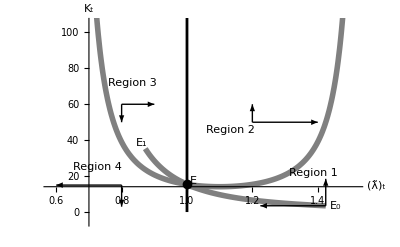
Using the expression for the optimal investment at time t, as given by (3), we obtain the following differential equation, which governs the motion of the stock of capital:
(4)	(d K^*)/(d t)=(((λ̃)_t-1)/χ)K_t^*,  K_0^*=K_0.

To analyze the dynamics of the system, we now construct a phase diagram. First, note that 
(5)	(d K^*)/(d t)=((λ̃)_t-1)/χ K_t^*≥ 0⟺(λ̃)_t≥1.

In the ((λ̃)_t,K_t)-plane, the points at which the capital stock rises are found on the right side of the vertical line (λ̃)_t=1 in the first quadrant. 

Next, using (3) in (2), we obtain
(6)	(d λ̃)/(d t)=r (λ̃)_t-(A_t F'[K_t^*]+1/2 χ (I_t^*/K_t^*)^2)
	=r (λ̃)_t-(A_t F'[K_t^*]+1/2 χ (((λ̃)_t-1)/χ)^2)
	=r (λ̃)_t-A_t F'[K_t^*]-1/(2χ)((λ̃)_t-1)^2.
Thus, (d λ̃)/dt≥ 0 if 
(7)	r (λ̃)_t-1/(2χ)((λ̃)_t-1)^2≥A_t F'[K_t^*].
Because F[K] is concave, F'[K], the marginal product of capital, is decreasing when K increases. Thus, the inequality in (7) is equivalent to the following inequality:
(8)	K_t^*≥ (F')^-1((r(λ̃)_t-1/(2χ) ((λ̃)_t-1)^2)/A_t),
and the current shadow price of capital (λ̃)_t will be rising if K_t^* is above the curve
	(λ̃)_t→K_t= (F')^-1((r(λ̃)_t-1/(2χ) ((λ̃)_t-1)^2)/A_t) 
in the first quadrant of the ((λ̃)_t,K_t)-plane. Note that the curve 
	(λ̃)_t→  (r(λ̃)_t-1/(2χ) ((λ̃)_t-1)^2)/A_t
is a an upside down parabola because the coefficient of the second-degree term is negative.. Thus, the curve
		(λ̃)_t→K_t= (F')^-1((r(λ̃)_t-1/(2χ) ((λ̃)_t-1)^2)/A_t)
is U-shaped in the ((λ̃)_t,K_t)-plane.

Suppose that A_t=A= constant. In the long-run equilibrium, the capital stock remains at the same level as time goes on, i.e., I_t^*=0, which, according to (3), implies that
(9)	 (λ̃)_t=λ̄=1.
Also, in the long-run equilibrium (d λ̃)/dt=0, and using (6), we obtain
(10)	K_t^*=K̄⟹ A F'[K̄]=r.

The following figure depicts the phase diagram that shows the motion of the cpaital stock and the shadow price of capital in the (K,λ̃)-plane. The vertical line with horizontal co-ordinate λ̃=1 and the U-shaped curve (λ̃)_t→(λ̃)_t→K_t= (F')^-1((r(λ̃)_t-1/(2χ) ((λ̃)_t-1)^2)/A_t)  cross each other at a single point labeled E, which represents the long-run equilibrium of the system. The two curves partitioned the first quadrant of the (K,λ̃)-plane into four regions, and the arrows in reach region shows the direction of the movement of the system, given that the system is found at that location in the phase diagram. 

	-Graphics-
In Region 2, the system diverges: both the capital stock and the shadow price of capital rises to infinity as time goes on. Such a scenario cannot occur under the optimal investment program, as explained in the discrete time version of the problem. In Region 2, both the stock of capital and the shadow price of capital falls to 0 in finite time, and the system will become incoherent in finite time, as explained in the discrete time version of the problem. Thus, under the optimal investment program the system is found either in Region 1 or Region 3. More specifically, if the initial capital stock is below its long-run value, the system will begin in Region 1, and then converges to the long-run equiliberium along the curve E_0 E. On the other hand, if the initial capital stock is above its long-run value, the system will begin in Region 3, and then converges to the long-run equiliberium along the curve E_1 E.

(b) To answer this question define

(11)	v[K,t]=max_((I_t)_(t≥ τ)) ∫_t^∞ ⅇ^(-r s)(A F[K_s]-I_s-1/2 χ I_s^2/K_ts)ⅆs
subject to
(12)	dK/ds=I_s,s≥ t,
K_t=K.

As defined, v[K,t] represents the present value of the stream of profits earned by the firm under the optimal investment program, given that it begins at time t with a capital stock of size K. When K=K_0,t=0, the problem constituted by (11) and (12) is reduced to the original problem that the firm need to solve.

Note that v[K,t]=ⅇ^-rt v[K,0], from which we obtain

(13)	D_2 v[K,t]=-r ⅇ^-rt v[K,0]=-r v[K,t].

Now for the problem constituted by (11) and (12), the Hamilton-Jacobi-Bellman equation is
(14)	0=max_I (ⅇ^(-r t)(A F[K]-I-1/2 χ I^2/K)+D_1 v[K,t]I+D_2 v[K,t]).

Applying (14) at a point (K_t^*,t) along the optimal trajectory of the original problem, we obtain
(15)	0=ⅇ^(-r t)(A F[K_t^*]-I_t^*-1/2 χ ((I_t^*)^2)/K_t^*)+λ_t I_t^*-r ⅇ^(-r t)v[K_t^*,0]
	=A F[K_t^*]-I_t^*-1/2 χ ((I_t^*)^2)/K_t^*+λ_t ⅇ^(r t)I_t^*-r v[K_t^*,0]. 
Note that in (15), λ_t=D_1 v[K_t^*,t] is the shadow price of capital along the optimal trajectory. Now the second line in (15) can be rewritten as follows
(16)	A F[K_t^*]-I_t^*-1/2 χ ((I_t^*)^2)/K_t^*+(λ̃)_t I_t^*=r v[K_t^*,0],
where (λ̃)_t=ⅇ^(r t)λ_t is the current (undiscounted) shadow price of capital.

Now consider a constant flow of profit equal to r v[K_t^*,0] starting from time t and stretching indefinitely into the future. The discounted value of this stream of profit - discounted back to time t - is v[K_t^*,0]. Also, note that v[K_t^*,0] represents the discounted value of the stream of profit - discounted only back to time t - obtained under the optimal investment program, given that the firm begins at time t with K_t^* as its stock of capital. Thus, r v[K_t^*,0] represents the net income of the firm at time t. Next, note that the left-hand side of (16) is the current Hamiltonian evaluated at time t along the optimal trajectory. The equality (16) asserts that the current Hamiltonian at any point on the optimal trajectory is equal to the firm’s income at that instant, and this income is the sum of the firm’s profit (A F[K_t^*]-I_t^*-1/2 χ ((I_t^*)^2)/K_t^*) and the value of the capital investment OverTilde[(λ]_t I_t^*) at that instant.

### The phase diagram

In the statement of the problem, the capital stock is denoted by K (upper-case). In Mathematica, K(upper-case) represents a some kind of name for certain functions. So, we use k(lower-case) to denote the capital stock in the Mathematica computations

```mathematica
F[k_]:=k^α
```

```mathematica
F[k]
```

k^α

```mathematica
F'[k]
```

k^(-1+α) α

The curve along which the current shadow price of capital does not vary: (d λ̃)/dt=0

```mathematica
eq[0]=A F'[k]==r λ̃-1/(2χ) (λ̃-1)^2
```

A k^(-1+α) α==-(-1+λ̃)^2/(2 χ)+r λ̃

```mathematica
s[0]=Solve[eq[0],k]//Flatten
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{k→(-(1/(2 χ)-r λ̃-(λ̃)/χ+(λ̃)^2/(2 χ))/(A α))^(1/(-1+α))}

```mathematica
m[1]=k/.s[0]
```

(-(1/(2 χ)-r λ̃-(λ̃)/χ+(λ̃)^2/(2 χ))/(A α))^(1/(-1+α))

```mathematica
m[1]/.λ̃-> Subscript[λ̃, t]
```

(-(1/(2 χ)-r (λ̃)_t-((λ̃)_t)/χ+((λ̃)_t^2)/(2 χ))/(A α))^(1/(-1+α))

The equation of the curve along which (d λ̃)/dt=0 is K_t=((-1/(2 χ)+r λ̃+(λ̃)/χ-(λ̃)^2/(2 χ))/(A α))^(1/(-1+α)). Above the curve, (λ̃)_t is rising; below the curve, (λ̃)_t is declining.

```mathematica
r=0.1;A=1.0;α=0.45;χ=1.0;
```

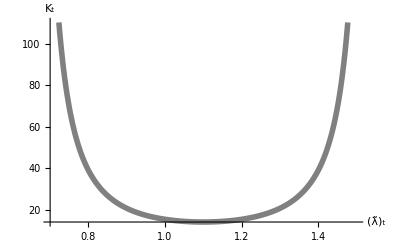

```mathematica
g[1]=Plot[m[1],{λ̃,0.7,1.5},AxesLabel->{"(λ̃)_t","K_t"},PlotStyle-> {{Thickness[0.01],GrayLevel[0.5]}}]
```

The curve along which the capital stock does not vary: dK/dt=0. Investment is positive, i.e., the capital stock is rising, on the right side of the vertical line λ̃=1; on the left side of this vertical line, the capital stock is declining because the firm dis-invests.

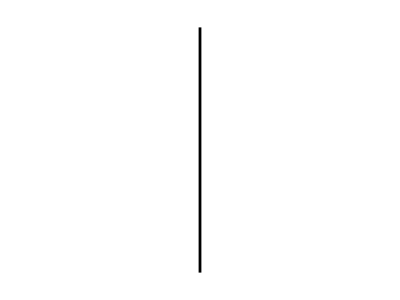

```mathematica
g[2]=Graphics[{AbsoluteThickness[2],Line[{{1,0},{1,190}}]}]
```

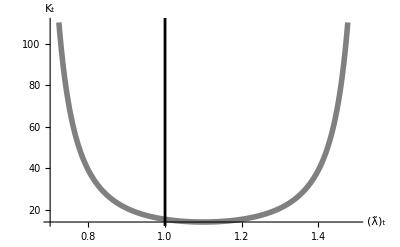

```mathematica
Show[g[1],g[2]]
```

#### The long-run equilibrium

```mathematica
λBar=1
```

1

```mathematica
kBar=m[1]/.λ̃-> λBar
```

15.4049

The time horizon

```mathematica
T=15;
```

```mathematica
ϵ=0.01;
```

#### Backward shooting from a point in the neighborhood of the long-run equilibrium

The time path of the solution (the curve E_0 E in the phase diagram) when the initial capital stock K_0 is below K̄, the long-run equilibrium level.

```mathematica
eq[1]=k'[t]==(λ̃[t]-1)/χ k[t]
```

k'[t]==1. k[t] (-1+λ̃[t])

```mathematica
eq[2]=λ̃'[t]==-A F'[k[t]]-1/(2 χ) (λ̃[t]-1)^2+r λ̃[t]
```

λ̃'[t]==-0.45/k[t]^0.55-0.5 (-1+λ̃[t])^2+0.1 λ̃[t]

```mathematica
s[1]=NDSolve[{eq[1],eq[2],k[T]==kBar-100 ϵ,λ̃[T]==λBar+ϵ},{k,λ̃},{t,0,T}]//Flatten
```

{k→InterpolatingFunction[{{0., 15.}}, <>],λ̃→InterpolatingFunction[{{0., 15.}}, <>]}

#### Test of solution

```mathematica
{k[0],λ̃[0]}/.s[1]
```

{3.49072,1.42451}

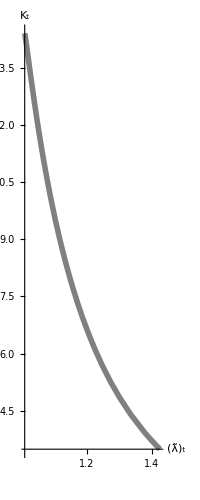

```mathematica
g[3]=ParametricPlot[{λ̃[t],k[t]}/.s[1],{t,0,T},AxesLabel->{"(λ̃)_t","K_t"},PlotStyle-> {{Thickness[0.01],GrayLevel[0.5]}}]
```

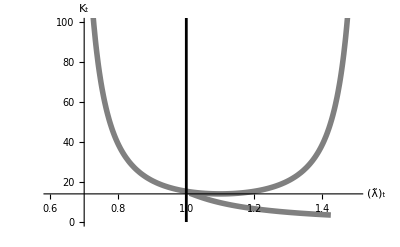

```mathematica
Show[g[1],g[2],g[3],PlotRange-> {{0.6,1.5},{0,100}}]
```

The time path of the solution (the curve E_1 E in the phase diagram) when the initial capital stock K_0 is higher than K̄, the long-run equilibrium level.

```mathematica
s[2]=NDSolve[{eq[1],eq[2],k[T]==kBar+100 ϵ,λ̃[T]==λBar-ϵ},{k,λ̃},{t,0,T}]//Flatten
```

{k→InterpolatingFunction[{{0., 15.}}, <>],λ̃→InterpolatingFunction[{{0., 15.}}, <>]}

```mathematica
{k[0],λ̃[0]}/.s[2]
```

{35.2854,0.87237}

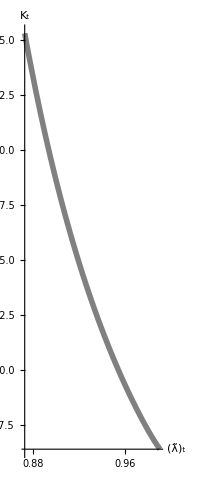

```mathematica
g[4]=ParametricPlot[{λ̃[t],k[t]}/.s[2],{t,0,T},AxesLabel->{"(λ̃)_t","K_t"},PlotStyle-> {{Thickness[0.01],GrayLevel[0.5]}}]
```

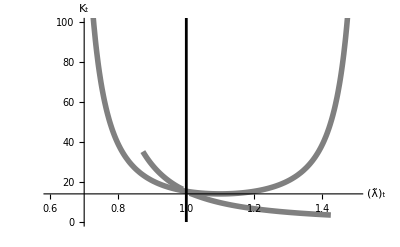

```mathematica
Show[g[1],g[2],g[3],g[4],PlotRange-> {{0.6,1.5},{0,100}}]
```

```mathematica
g[5]=Graphics[Text["E",{λBar+0.02,kBar+2}]];
```

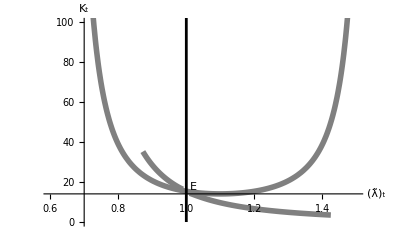

```mathematica
Show[g[1],g[2],g[3],g[4],g[5],PlotRange-> {{0.6,1.5},{0,100}}]
```

```mathematica
g[6]=Graphics[Text["E_0",{λ̃[0]+0.03,k[0]}/.s[1]]];
```

```mathematica
g[7]=Graphics[Text["E_1",{λ̃[0]-0.01,k[0]+3}/.s[2]]];
```

```mathematica
g[8]=Graphics[{AbsolutePointSize[7],Point[{λBar,kBar}]}];
```

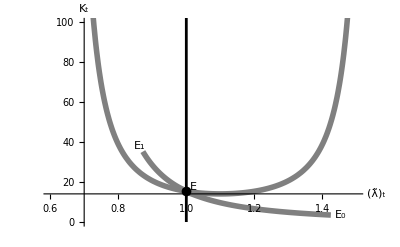

```mathematica
Show[g[1],g[2],g[3],g[4],g[5],g[6],g[7],g[8],PlotRange-> {{0.6,1.5},{0,100}}]
```

```mathematica
g[9]=Graphics[Arrow[{{λ̃[0],k[0]}/.s[1],{λ̃[0]-0.2,k[0]}/.s[1]}]];
```

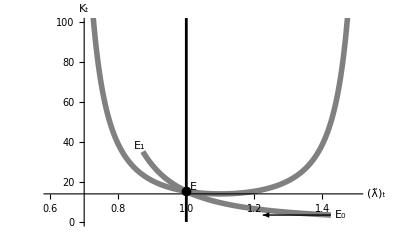

```mathematica
Show[g[1],g[2],g[3],g[4],g[5],g[6],g[7],g[8],g[9],PlotRange-> {{0.6,1.5},{0,100}}]
```

```mathematica
g[10]=Graphics[{Arrow[{{0.8,15},{0.6,15}}],Arrow[{{0.8,15},{0.8,3}}]}];
```

```mathematica
g[11]=Graphics[{Arrow[{{0.8,60},{0.8,50}}],Arrow[{{0.8,60},{0.9,60}}]}];
```

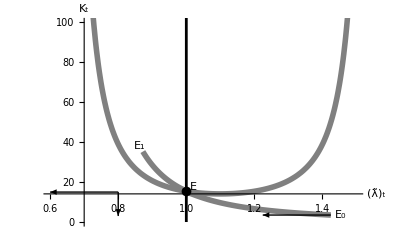

```mathematica
Show[g[1],g[2],g[3],g[4],g[5],g[6],g[7],g[8],g[9],g[10],PlotRange-> {{0.6,1.5},{0,100}}]
```

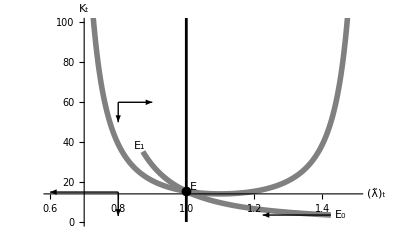

```mathematica
Show[g[1],g[2],g[3],g[4],g[5],g[6],g[7],g[8],g[9],g[10],g[11],PlotRange-> {{0.6,1.5},{0,100}}]
```

```mathematica
g[12]=Graphics[{Arrow[{{1.2,50},{1.4,50}}],Arrow[{{1.2,50},{1.2,60}}]}];
```

```mathematica
g[13]=Graphics[Arrow[{{λ̃[0],k[0]}/.s[1],{λ̃[0],k[0]+15}/.s[1]}]];
```

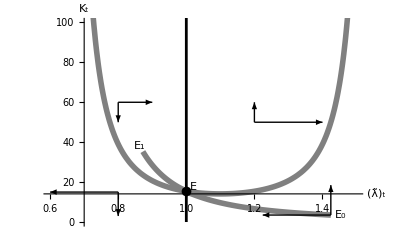

```mathematica
Show[g[1],g[2],g[3],g[4],g[5],g[6],g[7],g[8],g[9],g[10],g[11],g[12],g[13],PlotRange-> {{0.6,1.5},{0,100}}]
```

```mathematica
ClearAll[F,eq,T,s,m,r,A,α,χ,T,ϵ,g,kBar,λBar]
```

6. Find a continuous function c:t→c_t,t≥0, to 
	minimize_((c_t)_(t≥0))∫_0^∞ (x_t^2+c_t^2)ⅆt 
	subject to (d x)/(d t)=-x_t + c_t, x_0=(x̄)_0.

```mathematica
ℋ=x^2+c^2+λ (-x+c)
```

c^2+x^2+(c-x) λ

```mathematica
D[ℋ,c]
```

2 c+λ

```mathematica
s[1]=Solve[%==0,c]//Flatten
```

{c→-λ/2}

```mathematica
D[ℋ,x]
```

2 x-λ

```mathematica
eq[1]=λ'[t]==-(%/.{x->x[t],λ->λ[t]})
```

λ'[t]==-2 x[t]+λ[t]

```mathematica
eq[2]=x'[t]==-x[t]+((c/.s[1])/.λ->λ[t])
```

x'[t]==-x[t]-λ[t]/2

```mathematica
s[2]=DSolve[{eq[1],eq[2],λ[0]==λ0,x[0]==OverBar[x0]},{λ[t],x[t]},t]//Flatten
```

{x[t]→-1/8 ⅇ^(-√2 t) (-√2 λ0+√2 ⅇ^(2 √2 t) λ0-4 OverBar[x0]-2 √2 OverBar[x0]-4 ⅇ^(2 √2 t) OverBar[x0]+2 √2 ⅇ^(2 √2 t) OverBar[x0]),λ[t]→1/4 ⅇ^(-√2 t) (2 λ0-√2 λ0+2 ⅇ^(2 √2 t) λ0+√2 ⅇ^(2 √2 t) λ0+2 √2 OverBar[x0]-2 √2 ⅇ^(2 √2 t) OverBar[x0])}

```mathematica
λ[t_]:=(Evaluate[λ[t]/.s[2]])
```

```mathematica
λ[t]
```

1/4 ⅇ^(-√2 t) (2 λ0-√2 λ0+2 ⅇ^(2 √2 t) λ0+√2 ⅇ^(2 √2 t) λ0+2 √2 OverBar[x0]-2 √2 ⅇ^(2 √2 t) OverBar[x0])

```mathematica
x[t_]:=Evaluate[x[t]/.s[2]]
```

```mathematica
x[t]
```

-1/8 ⅇ^(-√2 t) (-√2 λ0+√2 ⅇ^(2 √2 t) λ0-4 OverBar[x0]-2 √2 OverBar[x0]-4 ⅇ^(2 √2 t) OverBar[x0]+2 √2 ⅇ^(2 √2 t) OverBar[x0])

```mathematica
x[t]=Collect[x[t],ⅇ^(√2 t)]
```

-1/8 ⅇ^(-√2 t) (-√2 λ0-4 OverBar[x0]-2 √2 OverBar[x0])-1/8 ⅇ^(√2 t) (√2 λ0-4 OverBar[x0]+2 √2 OverBar[x0])

```mathematica
Coefficient[x[t],ⅇ^(√2 t)]
```

-λ0/(4 √2)+OverBar[x0]/2-OverBar[x0]/(2 √2)

```mathematica
Solve[%==0,λ0]//Flatten//Simplify
```

{λ0→2 (-1+√2) OverBar[x0]}

```mathematica
λ0=(λ0/.%)
```

2 (-1+√2) OverBar[x0]

```mathematica
λ[t]//Simplify
```

2 (-1+√2) ⅇ^(-√2 t) OverBar[x0]

```mathematica
c[t_]:=(c/.s[1]/.λ->λ[t])//Simplify
```

```mathematica
c[t]
```

-(-1+√2) ⅇ^(-√2 t) OverBar[x0]

```mathematica
v=∫_0^∞ (x[t]^2+c[t]^2)ⅆt
```

(-1+√2) OverBar[x0]^2

```mathematica
ClearAll[ℋ,s,eq,λ,λ0,x,c,v]
```

7. Consider a system whose state vector at time t  is denoted by x(t)=(x_1(t),x_2(t)),0≤t≤18. Let u:t→u(t),0≤t≤18, be a continuous control function that satisties the constraint  0≤u(t)≤1 for 0≤t≤18. The dynamics of the system under u is governed by the following system of differential equations:
	(d x_1)/(d t)=2 x_1[t]+x_2[t ]+u[t], x_1[0]=(x̄)_1[0]
(d x_2)/(d t)=4 x_1[t]-2u[t],    x_2[0]=(x̄)_2[0].
Find the control that maximizes the terminal payoff 8x_1[18]+4x_2[18].

```mathematica
ℋ=λ[1] (2 x[1]+x[2]+u)+λ[2] (4 x[1]-2u)
```

(u+2 x[1]+x[2]) λ[1]+(-2 u+4 x[1]) λ[2]

```mathematica
ℋ=Collect[ℋ,u]
```

2 x[1] λ[1]+x[2] λ[1]+u (λ[1]-2 λ[2])+4 x[1] λ[2]

The adjoint equations

```mathematica
D[ℋ, x[1]]
```

2 λ[1]+4 λ[2]

```mathematica
%/.{x[1]-> x[1][t],x[2]->  x[2][t],λ[1]-> λ[1][t],λ[2]-> λ[2][t]}
```

2 λ[1][t]+4 λ[2][t]

```mathematica
eq[1]=λ[1]'[t]==-%
```

λ[1]'[t]==-2 λ[1][t]-4 λ[2][t]

```mathematica
D[ℋ, x[2]]
```

λ[1]

```mathematica
%/.{x[1]-> x[1][t],x[2]->  x[2][t],λ[1]-> λ[1][t],λ[2]-> λ[2][t]}
```

λ[1][t]

```mathematica
eq[2]=λ[2]'[t]==-%
```

λ[2]'[t]==-λ[1][t]

Let us tell Mathematica to solve the system of adjoint equations with the final conditions represented by (5).

```mathematica
s[0]=DSolve[{eq[1],eq[2],λ[1][18]==8,λ[2][18]==4},{λ[1][t],λ[2][t]},t]//Flatten
```

{λ[1][t]→-4/5 ⅇ^(18-18 √5-t-√5 t) (-5 ⅇ^(36 √5)-3 √5 ⅇ^(36 √5)-5 ⅇ^(2 √5 t)+3 √5 ⅇ^(2 √5 t)),λ[2][t]→1/(√5)2 ⅇ^(18-18 √5-t-√5 t) (ⅇ^(36 √5)+√5 ⅇ^(36 √5)-ⅇ^(2 √5 t)+√5 ⅇ^(2 √5 t))}

The coefficient of u in the Hamiltonian (7) is

```mathematica
m[t_]:=Evaluate[(λ[1][t]-2 λ[2][t])/.s[0]]
```

```mathematica
m[t]
```

-1/(√5)4 ⅇ^(18-18 √5-t-√5 t) (ⅇ^(36 √5)+√5 ⅇ^(36 √5)-ⅇ^(2 √5 t)+√5 ⅇ^(2 √5 t))-4/5 ⅇ^(18-18 √5-t-√5 t) (-5 ⅇ^(36 √5)-3 √5 ⅇ^(36 √5)-5 ⅇ^(2 √5 t)+3 √5 ⅇ^(2 √5 t))

```mathematica
m[0]
```

-4/5 ⅇ^(18-18 √5) (-5+3 √5-5 ⅇ^(36 √5)-3 √5 ⅇ^(36 √5))-1/(√5)4 ⅇ^(18-18 √5) (-1+√5+ⅇ^(36 √5)+√5 ⅇ^(36 √5))

```mathematica
%//N
```

7.09449×10^25

```mathematica
m[18]//N
```

0.

To find the sign of the coefficient of λ_1[t]-2 λ_2[t], plot m[t].

```mathematica
Plot[m[t],{t,0,18}, AxesLabel-> {"t","λ_1[t]-2λ_2[t]"}]
```

-Graphics-

As can be seen from the preceding figure, t→ m_t,0≤ t≤ 18, is strictly decreasing from 7.09449×10^25 to 0 as t rises from 0 to 18. Thus u_t^*=1,0≤ t≤ 1. A more rigorous argument is to show that the derivative of m_t with respect to t is negative as follows:

```mathematica
m'[t]//FullSimplify
```

16/5 ⅇ^(18-t) (-5 Cosh[√5 (-18+t)]+√5 Sinh[√5 (-18+t)])

Let us determine the sign of the preceding expression.

```mathematica
α=√5 (-18+t)
```

√5 (-18+t)

We know that the hyperbolic functions Cosh[α] and Sinh[α] are defined by
	cosh(α)==1/2 (ⅇ^α+ⅇ^-α), sinh(α)==1/2 (ⅇ^α-ⅇ^-α).
The sign of the derivative m'[t] is the sign of test.

```mathematica
test=-5 1/2 (ⅇ^α+ⅇ^-α)+√5 1/2 (ⅇ^α-ⅇ^α)
```

-5/2 (ⅇ^(-√5 (-18+t))+ⅇ^(√5 (-18+t)))

Clearly, test<0. Thus, the optimal control at time t is

```mathematica
u[t]=1
```

1

The state equations are

```mathematica
eq[3]=x[1]'[t]==2 x[1][t]+x[2][t]+u[t]
```

x[1]'[t]==1+2 x[1][t]+x[2][t]

```mathematica
eq[4]=x[2]'[t]==4 x[1][t]-2u[t]
```

x[2]'[t]==-2+4 x[1][t]

```mathematica
s[1]=DSolve[{eq[3],eq[4],x[1][0]==x10,x[2][0]==x20},{x[1][t],x[2][t]},t]//Flatten
```

{x[1][t]→1/20 ⅇ^(t-√5 t-(1+√5) t) (10 ⅇ^(2 √5 t)-5 ⅇ^((1+√5) t)-3 √5 ⅇ^((1+√5) t)-5 ⅇ^(2 √5 t+(1+√5) t)+3 √5 ⅇ^(2 √5 t+(1+√5) t)+10 ⅇ^((1+√5) t) x10-2 √5 ⅇ^((1+√5) t) x10+10 ⅇ^(2 √5 t+(1+√5) t) x10+2 √5 ⅇ^(2 √5 t+(1+√5) t) x10-2 √5 ⅇ^((1+√5) t) x20+2 √5 ⅇ^(2 √5 t+(1+√5) t) x20),x[2][t]→1/10 ⅇ^(t-√5 t-(1+√5) t) (-20 ⅇ^(2 √5 t)+10 ⅇ^((1+√5) t)+4 √5 ⅇ^((1+√5) t)+10 ⅇ^(2 √5 t+(1+√5) t)-4 √5 ⅇ^(2 √5 t+(1+√5) t)-4 √5 ⅇ^((1+√5) t) x10+4 √5 ⅇ^(2 √5 t+(1+√5) t) x10+5 ⅇ^((1+√5) t) x20+√5 ⅇ^((1+√5) t) x20+5 ⅇ^(2 √5 t+(1+√5) t) x20-√5 ⅇ^(2 √5 t+(1+√5) t) x20)}

```mathematica
s[1]=s[1]//FullSimplify
```

{x[1][t]→1/20 ⅇ^(-2 √5 t) (10 ⅇ^(2 √5 t)-ⅇ^((1+√5) t) (5+3 √5+2 (-5+√5) x10+2 √5 x20)+ⅇ^(t+3 √5 t) (-5+3 √5+2 (5+√5) x10+2 √5 x20)),x[2][t]→1/10 ⅇ^(-2 √5 t) (-20 ⅇ^(2 √5 t)+ⅇ^(t+3 √5 t) (10-4 √5+4 √5 x10+5 x20-√5 x20)+ⅇ^((1+√5) t) (10+4 √5-4 √5 x10+(5+√5) x20))}

```mathematica
x[1][t_]:=Evaluate[x[1][t]/.s[1]]
x[2][t_]:=Evaluate[x[2][t]/.s[1]]
```

The optimal payoff is

```mathematica
x[1][18]
```

1/20 ⅇ^(-36 √5) (10 ⅇ^(36 √5)-ⅇ^(18 (1+√5)) (5+3 √5+2 (-5+√5) x10+2 √5 x20)+ⅇ^(18+54 √5) (-5+3 √5+2 (5+√5) x10+2 √5 x20))

```mathematica
x[2][18]
```

1/10 ⅇ^(-36 √5) (-20 ⅇ^(36 √5)+ⅇ^(18+54 √5) (10-4 √5+4 √5 x10+5 x20-√5 x20)+ⅇ^(18 (1+√5)) (10+4 √5-4 √5 x10+(5+√5) x20))

```mathematica
v=8 x[1][18]+4 x[2][18]
```

2/5 ⅇ^(-36 √5) (10 ⅇ^(36 √5)-ⅇ^(18 (1+√5)) (5+3 √5+2 (-5+√5) x10+2 √5 x20)+ⅇ^(18+54 √5) (-5+3 √5+2 (5+√5) x10+2 √5 x20))+2/5 ⅇ^(-36 √5) (-20 ⅇ^(36 √5)+ⅇ^(18+54 √5) (10-4 √5+4 √5 x10+5 x20-√5 x20)+ⅇ^(18 (1+√5)) (10+4 √5-4 √5 x10+(5+√5) x20))

```mathematica
v//N//FullSimplify
```

2.19232×10^25+1.85736×10^26 x10+5.73957×10^25 x20

```mathematica
ClearAll[x,u,λ,v,eq,ℋ,s,m,α,test]
```